```mathematica
1+1
```

2

## Input

All volumes in units of m^3
All charging/discharging rates in units of m^3/h
All boil-off rates in units of percentage/day

```mathematica
LNGTerminals=<|"Golden Pass"-> <|"LatLong"->GeoPosition[{29.761564,-93.929215}], "Currency"-> "USD", "Type"->"Liquification and Export", "Total Terminal Storage Capacity"->Quantity[350000, ("Meters")^3], "Daily Production"->Quantity[5000, ("Meters")^3/"Days"],"Inventory"-> Quantity[100000, ("Meters")^3],  "Price"-> 4.1|>, "Gate LNG Terminal Netherland"-><|"LatLong"->GeoPosition[{51.9718, 4.0755}], "Currency"->"EUR", "Type"->"Import and Re-gasification", "Total Terminal Storage Capacity"->Quantity[540000, ("Meters")^3], "Price"-> 4.0|>, "Arun LNG Terminal and Plant Indonesia"-><|"LatLong"->GeoPosition[{5.2234, 97.083}], "Currency"->"Rupiah", "Type"->"Import and Re-gasification","Total Terminal Storage Capacity"->Quantity[635000, ("Meters")^3], "Price"->6.2 |>, "Rudong Jiangsu LNG Terminal China"-><|"LatLong"->GeoPosition[{32.5292,121.428}], "Currency"->"Yuan Renminbi", "Type"->"Import and Re-gasification","Total Terminal Storage Capacity"->Quantity[680000,("Meters")^3] , "Price"-> 6.5|>,
"PNG LNG Terminal Papua New Guinea"-><|"LatLong"->GeoPosition[{-9.33862,147.01825}], "Currency"->"Kina", "Type"->"Liquification and Export","Total Terminal Storage Capacity"->Quantity[320000,("Meters")^3], "Daily Production"->Quantity[2500, ("Meters")^3/"Days"],"Inventory"-> Quantity[320000, ("Meters")^3], "Price"->3.9 |>|>;
```

```mathematica
GeoMarker[#["LatLong"]] & /@ LNGTerminals
```

```mathematica
GeoGraphics[GeoMarker[#["LatLong"]] & /@ LNGTerminals, GeoRange->All]
```

```mathematica
LNGVessels=<|"WSD50"-><|"Speed"->Quantity[15.0, "NauticalMiles"/ "Hours"], "Capacity"->Quantity[20000, ("Meters")^3], "Maximum loading rate"->Quantity[ 1250, ("Meters")^3/"Days"], "Maimum discharge rate"->Quantity[1250, ("Meters")^3/"Days"], "Boil-off rate"->0.12, "Position"->GeoPosition[{58.97,5.71}], "Inventory"->Quantity[0, ("Meters")^3], "DailyFixedCost"-> 100|>, "TGE"-><|"Speed"->Quantity[16.0, "NauticalMiles"/ "Hours"], "Capacity"->Quantity[30000, ("Meters")^3], "Maximum loading rate"->Quantity[2000, ("Meters")^3/"Days"] ,"Maximum discharge rate"->Quantity[2500, ("Meters")^3/"Days"], "Boil-off rate"->0.19, "Position"->GeoPosition[{58.97,5.71}], "Inventory"->Quantity[0, ("Meters")^3], "DailyFixedCost"->150|>, "Leissner"-><|"Speed"->Quantity[13.0, "NauticalMiles"/ "Hours"], "Capacity"->Quantity[75000, ("Meters")^3], "Maximum loading rate"->Quantity[1000, ("Meters")^3/"Days"], "Maximum discharge rate"->Quantity[1000, ("Meters")^3/"Days"], "Boil-off rate"->0.15, "Position"->GeoPosition[{58.97,5.71}], "Inventory"->Quantity[0, ("Meters")^3], "DailyFixedCost"->200|>, "Tembek"-><|"Capacity"->Quantity[216100, ("Meters")^3], "Maximum loading rate"->Quantity[2600 , ("Meters")^3/"Days"],"Maximum discharge rate"->Quantity[1300, ("Meters")^3/"Days"], "Boil-off rate"->0, "Position"->GeoPosition[{58.97,5.71}], "Speed"-> Quantity[16.7, "NauticalMiles"/ "Hours"], "Inventory"->Quantity[0,("Meters")^3], "DailyFixedCost"-> 250|>|>;
```

```mathematica
GeoGraphics[GeoMarker[#["Position"]] & /@ LNGVessels, GeoRange->All]
```

```mathematica
Dataset[LNGTerminals]
```

Dataset[<>]

```mathematica
Dataset[LNGVessels]
```

Dataset[<>]

```mathematica
GeoDistance[{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]},UnitSystem->"NauticalMiles"]/LNGVessels["WSD50"]["Speed"]
```

278.707 h

```mathematica
{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]}
```

{GeoPosition[{58.97,5.71}],GeoPosition[{29.7616,-93.9292}]}

```mathematica
Tuples[{Keys[LNGVessels], Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]], Keys[Select[LNGTerminals, #Type=="Import and Re-gasification" &]]}]
```

{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China},{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China},{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China},{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China},{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China},{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China},{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China},{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}

```mathematica
Outer[{#1, #2, #3}&, Keys[LNGVessels], Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]], Keys[Select[LNGTerminals, #Type=="Import and Re-gasification" &]]]
```

{{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}}}

```mathematica
Tuples[Outer[{#1, #2, #3}&, Keys[LNGVessels], Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]], Keys[Select[LNGTerminals, #Type=="Import and Re-gasification" &]], 1, 1, 1]]
```

{{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,Golden Pass,Gate LNG Terminal Netherland},{WSD50,Golden Pass,Arun LNG Terminal and Plant Indonesia},{WSD50,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,Golden Pass,Gate LNG Terminal Netherland},{TGE,Golden Pass,Arun LNG Terminal and Plant Indonesia},{TGE,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,Golden Pass,Gate LNG Terminal Netherland},{Leissner,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Leissner,Golden Pass,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,Golden Pass,Gate LNG Terminal Netherland},{Tembek,Golden Pass,Arun LNG Terminal and Plant Indonesia},{Tembek,Golden Pass,Rudong Jiangsu LNG Terminal China}}},{{{WSD50,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{WSD50,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{WSD50,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{TGE,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{TGE,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{TGE,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Leissner,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Leissner,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Leissner,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}},{{Tembek,PNG LNG Terminal Papua New Guinea,Gate LNG Terminal Netherland},{Tembek,PNG LNG Terminal Papua New Guinea,Arun LNG Terminal and Plant Indonesia},{Tembek,PNG LNG Terminal Papua New Guinea,Rudong Jiangsu LNG Terminal China}}}}

```mathematica
v={v1, v2, v3};
p={p1, p2, ""};
m={m1, m2, m3};
```

```mathematica
Tuples[{v, p, m}]
```

{{v1,p1,m1},{v1,p1,m2},{v1,p1,m3},{v1,p2,m1},{v1,p2,m2},{v1,p2,m3},{v1,p3,m1},{v1,p3,m2},{v1,p3,m3},{v2,p1,m1},{v2,p1,m2},{v2,p1,m3},{v2,p2,m1},{v2,p2,m2},{v2,p2,m3},{v2,p3,m1},{v2,p3,m2},{v2,p3,m3},{v3,p1,m1},{v3,p1,m2},{v3,p1,m3},{v3,p2,m1},{v3,p2,m2},{v3,p2,m3},{v3,p3,m1},{v3,p3,m2},{v3,p3,m3}}

```mathematica
Tuples[{v, p}]/. {a_,b_}->a->b
```

{v1→p1,v1→p2,v1→p3,v2→p1,v2→p2,v2→p3,v3→p1,v3→p2,v3→p3}

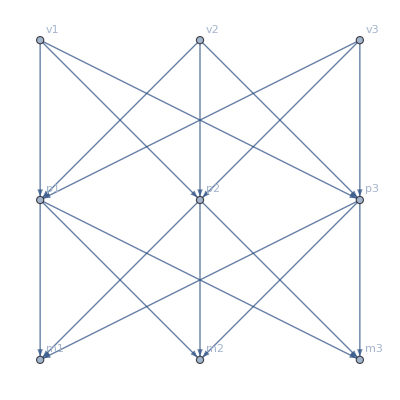

```mathematica
Graph[Join[Tuples[{v, p}]/. {a_,b_}->a->b, Tuples[{p, m}]/. {a_,b_}->a->b], VertexLabels->"Name"]
```

```mathematica
FindPath[Out[34], v1, m1, Infinity, All]
```

{{v1,p3,m1},{v1,p2,m1},{v1,p1,m1}}

```mathematica
Permutations[v]
```

{{v1,v2,v3},{v1,v3,v2},{v2,v1,v3},{v2,v3,v1},{v3,v1,v2},{v3,v2,v1}}

```mathematica
Permutations[p]
```

{{p1,p2},{p2,p1}}

```mathematica
Permutations[m]
```

{{m1,m2,m3},{m1,m3,m2},{m2,m1,m3},{m2,m3,m1},{m3,m1,m2},{m3,m2,m1}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ]
```

{{{v1,p1},{v2,p2},{v3,}},{{v1,p1},{v2,},{v3,p2}},{{v1,p2},{v2,p1},{v3,}},{{v1,p2},{v2,},{v3,p1}},{{v1,},{v2,p1},{v3,p2}},{{v1,},{v2,p2},{v3,p1}}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ], Permutations[m], 1, 1], 1]]
```

{{{{v1,p1},m1},{{v2,p2},m2},{{v3,},m3}},{{{v1,p1},m1},{{v2,p2},m3},{{v3,},m2}},{{{v1,p1},m2},{{v2,p2},m1},{{v3,},m3}},{{{v1,p1},m2},{{v2,p2},m3},{{v3,},m1}},{{{v1,p1},m3},{{v2,p2},m1},{{v3,},m2}},{{{v1,p1},m3},{{v2,p2},m2},{{v3,},m1}},{{{v1,p1},m1},{{v2,},m2},{{v3,p2},m3}},{{{v1,p1},m1},{{v2,},m3},{{v3,p2},m2}},{{{v1,p1},m2},{{v2,},m1},{{v3,p2},m3}},{{{v1,p1},m2},{{v2,},m3},{{v3,p2},m1}},{{{v1,p1},m3},{{v2,},m1},{{v3,p2},m2}},{{{v1,p1},m3},{{v2,},m2},{{v3,p2},m1}},{{{v1,p2},m1},{{v2,p1},m2},{{v3,},m3}},{{{v1,p2},m1},{{v2,p1},m3},{{v3,},m2}},{{{v1,p2},m2},{{v2,p1},m1},{{v3,},m3}},{{{v1,p2},m2},{{v2,p1},m3},{{v3,},m1}},{{{v1,p2},m3},{{v2,p1},m1},{{v3,},m2}},{{{v1,p2},m3},{{v2,p1},m2},{{v3,},m1}},{{{v1,p2},m1},{{v2,},m2},{{v3,p1},m3}},{{{v1,p2},m1},{{v2,},m3},{{v3,p1},m2}},{{{v1,p2},m2},{{v2,},m1},{{v3,p1},m3}},{{{v1,p2},m2},{{v2,},m3},{{v3,p1},m1}},{{{v1,p2},m3},{{v2,},m1},{{v3,p1},m2}},{{{v1,p2},m3},{{v2,},m2},{{v3,p1},m1}},{{{v1,},m1},{{v2,p1},m2},{{v3,p2},m3}},{{{v1,},m1},{{v2,p1},m3},{{v3,p2},m2}},{{{v1,},m2},{{v2,p1},m1},{{v3,p2},m3}},{{{v1,},m2},{{v2,p1},m3},{{v3,p2},m1}},{{{v1,},m3},{{v2,p1},m1},{{v3,p2},m2}},{{{v1,},m3},{{v2,p1},m2},{{v3,p2},m1}},{{{v1,},m1},{{v2,p2},m2},{{v3,p1},m3}},{{{v1,},m1},{{v2,p2},m3},{{v3,p1},m2}},{{{v1,},m2},{{v2,p2},m1},{{v3,p1},m3}},{{{v1,},m2},{{v2,p2},m3},{{v3,p1},m1}},{{{v1,},m3},{{v2,p2},m1},{{v3,p1},m2}},{{{v1,},m3},{{v2,p2},m2},{{v3,p1},m1}}}

```mathematica
URLExecute[HTTPRequest["https://api.aquaplot.com/v1/route/from/32.67333984375/33.17434155100208/to/35.92529296875/24.806681353851964"]]
```

## Junk

### Define the region of all seas.

https://mathematica.stackexchange.com/questions/104407/geographics-path-within-a-country/104416#104416

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{51.9718, 4.0755}]}]
```

TravelDirections::noroute: Cannot compute path with travel method Driving between locations {GeoPosition[{29.7616,-93.9292}],GeoPosition[{51.9718,4.0755}]}.

$Failed

```mathematica
GeoGraphics[GeoMarker @ {GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.761564,-93.929215}]}]
```

-Graphics-

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.76156,-93.929215}]}, TravelMethod->"Walking"]
```

TravelDirectionsData[…]

```mathematica
GeoGraphics[LinguisticAssistant]
```

-Graphics-

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
Entity["Ocean","AtlanticOcean"]
```

Atlantic Ocean

```mathematica
allPonds=GeoGroup[{Entity["Ocean","AtlanticOcean"], Entity["Ocean","AdriaticSea"],Entity["Ocean","AegeanSea"],Entity["Ocean","AlboranSea"],Entity["Ocean","ArgentineSea"],Entity["Ocean","BayBiscay"],Entity["Ocean","BayBothnia"],Entity["Ocean","BayCampeche"],Entity["Ocean","BayFundy"],Entity["Ocean","BalticSea"],Entity["Ocean","BlackSea"],Entity["Ocean","BothnianSea"],Entity["Ocean","CaribbeanSea"],Entity["Ocean","CelticSea"],Entity["Ocean","CentralBalticSea"],Entity["Ocean","ChesapeakeBay"],Entity["Ocean","EnglishChannel"],Entity["Ocean","GulfBothnia"],Entity["Ocean","GulfGuinea"],Entity["Ocean","GulfFinland"],Entity["Ocean","GulfMexico"],Entity["Ocean","GulfSidra"],Entity["Ocean","GulfSaintLawrence"],Entity["Ocean","GulfVenezuela"],Entity["Ocean","IonianSea"],Entity["Ocean","LigurianSea"],Entity["Ocean","IrishSea"],Entity["Ocean","MarmaraSea"],Entity["Ocean","MediterraneanSea"],Entity["Ocean","MirtoonSea"],Entity["Ocean","NorthSea"],Entity["Ocean","SeaAzov"],Entity["Ocean","SeaCrete"],Entity["Ocean","SeaTheHebrides"],Entity["Ocean","SargassoSea"],Entity["Ocean","TampaBay"],Entity["Ocean","ThracianSea"],Entity["Ocean","TyrrhenianSea"],,}]
```

GeoGroup[{Atlantic Ocean,Adriatic Sea,Aegean Sea,Alboran Sea,Argentine Sea,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Baltic Sea,Black Sea,Bothnian Sea,Caribbean Sea,Celtic Sea,Central Baltic Sea,Chesapeake Bay,English Channel,Gulf of Bothnia,Gulf of Guinea,Gulf of Finland,Gulf of Mexico,Gulf of Sidra,Gulf of Saint Lawrence,Gulf of Venezuela,Ionian Sea,Ligurian Sea,Irish Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,North Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Sargasso Sea,Tampa Bay,Thracian Sea,Tyrrhenian Sea}]

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
pts=Flatten[poly[[1, 1]], 1];
```

```mathematica
line=Polygon[Range[##]]&@@@Partition[{1}~Join~Most[Riffle[Accumulate[Length/@#],1+Accumulate[Length/@#]]&@poly[[1,1]]],2];
```

```mathematica
aquifer=Quiet@DiscretizeRegion[MeshRegion[pts,line],MaxCellMeasure->.004];
```

```mathematica
GeoGraphics[aquifer]
```

-Graphics-

```mathematica
allPonds=Cases[Union[Flatten[Join[EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","BorderingBodiesOfWater"]], EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","Basins"]]], 1]], Entity[___]]
```

{Adriatic Sea,Aegean Sea,Alboran Sea,Amundsen Gulf,Andaman Sea,Arabian Sea,Arafura Sea,Argentine Sea,Baffin Bay,Balearic Sea,Bali Sea,Baltic Sea,Banda Sea,Barents Sea,Bay of Bengal,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Beaufort Sea,Bering Sea,Bismarck Sea,Black Sea,Bohai Sea,Bohol Sea,Bothnian Sea,Cambridge Bay,Camotes Sea,Caribbean Sea,Celebes Sea,Celtic Sea,Central Baltic Sea,Ceram Sea,Chesapeake Bay,Chilean Sea,Chukchi Sea,Coastal Waters Of Southeast Alaska and British Columbia,Cold Bay,Coral Sea,Davis Strait,Denmark Strait,East China Sea,East Siberian Sea,English Channel,Flores Sea,Great Australian Bight,Greenland Sea,Gulf of Aden,Gulf of Alaska,Gulf of Bothnia,Gulf of California,Gulf of Carpentaria,Gulf of Finland,Gulf of Guinea,Gulf of Mexico,Gulf of Saint Lawrence,Gulf of Sidra,Gulf of Thailand,Gulf of Venezuela,Halmahera Sea,Hudson Bay,Indian Ocean,Inner Seas Off the West Coast of Scotland,Ionian Sea,Irish Sea,James Bay,Sea of Japan,Java Sea,Kara Sea,Kara Strait,Koro Sea,Labrador Sea,Laccadive Sea,Laptev Sea,Ligurian Sea,Lincoln Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,Molucca Sea,Mozambique Channel,North Atlantic Ocean,North Pacific Ocean,North Sea,Northwest Passages,Norwegian Sea,Okhotsk Sea,Persian Gulf,Philippine Sea,Red Sea,Rio De La Plata,Salish Sea,Sargasso Sea,Savu Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Seto Inland Sea,Solomon Sea,South Atlantic Ocean,South China Sea,Southern Ocean,South Pacific Ocean,Strait of Gibraltar,Sulu Sea,Tampa Bay,Tasman Sea,Thracian Sea,Timor Sea,Tyrrhenian Sea,White Sea,Yellow Sea}